```mathematica
dat=Import["/Users/jorisvanlammeren/Documents/Studie/Scriptie/JorisVLammeren/Data/Svalbard_S6_input.txt","Table"];
```

```mathematica
Lat=Take[dat,All,{5,6}];
```

```mathematica
data1=Drop[Lat,1];
```

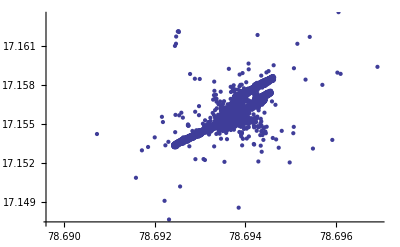

```mathematica
ListPlot[data1]
```

```mathematica
Lat1=Take[dat,All,{5}];
Lat11=Drop[Lat1,1];
Latecht=Transpose[Lat11][[1]];
```

```mathematica
Lot1=Take[dat,All,{6}];
Lot11=Drop[Lot1,1];
Lotecht=Transpose[Lot11][[1]];
```

```mathematica
List[a]
```

{a}

```mathematica
For[l=1,Latecht[[l]]>75,l++,Print[[Latecht[[l+1]]-Latecht[[l]]]]]
```

Part::pspec: Part specification -0.000014 is neither an integer nor a list of integers.

Part::pspec: Part specification 3.33333×10^-6 is neither an integer nor a list of integers.

Part::pspec: Part specification -0.0000141667 is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.